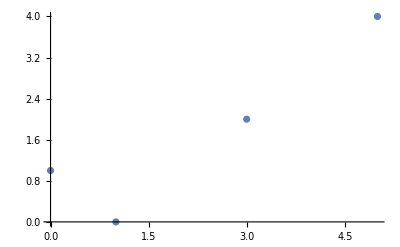

```mathematica
data={{0,1},{1,0},{3,2},{5,4}};
ListPlot[data]
```

```mathematica
p=Fit[data,{1,x},x]
```

```mathematica
FindFit[data,a x Log[b+c x],{a,b,c},x]
```

{a→0.197246,b→-13.1835,c→14.1835}

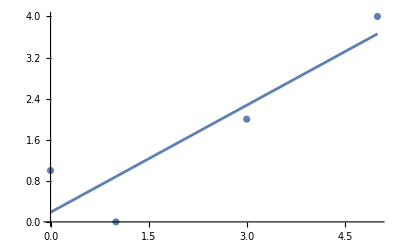

```mathematica
Show[{ListPlot[data],Plot[p,{x,0,5}]}]
```